# LU Decomposition of A

Just as a reminder the LU decomposition (which underlies efficient Gaussian Elimination) factors a matrix into a Lower and Upper triangular part.  LU decompositions are ALWAYS pivoted with row pivoting being the most common implemented version.  Code always packs the two pieces together and provides an estimate of a condition number.

```mathematica
n=321;
A=RandomReal[{-1,1},{n,n}];
{LU,p,c}=LUDecomposition[A];
L=LowerTriangularize[LU,-1]+IdentityMatrix[n];
U=UpperTriangularize[LU];
TabView[Map[MatrixForm,{A,L.U,A⟦p⟧}]];
TabView[Map[MatrixPlot,{L,U}]]
{Norm[A⟦p⟧-L.U],c, MinMax[SingularValueList[A]]}
```

12

{5.87959×10^-14,32021.9,{0.0125072,20.2886}}

## Fill In

The LU Decomposition of a sparse matrix A has more (frequently lost more) non-zero entries than A.  This problem is called fill-in or just fill!

```mathematica
n=123;
nz=3n;
A=SparseArray[Band[{1,1}]:> RandomReal[{0.1,10}],{n,n}];
Do[ {i,j}=RandomInteger[{1,n},{2}];
A⟦i,j⟧+=RandomReal[{-1,1}],
{nz}]
A=Normal[A];
{LU,p,c}=LUDecomposition[A];
L=LowerTriangularize[LU,-1]+IdentityMatrix[n];
U=UpperTriangularize[LU];
TabView[Map[MatrixPlot,{A,L,U}]]
```

123

Of course, this still satisfies A[[p]]-L.U=0 but it is at the cost of a lot of fill.  The idea of an incomplete decomposition is to trade A-L.U≈0 for a lot less fill!  The question is how to pick the values to not worry about.

## ILU

Mathematica has an undocumented command “SparseArray`SparseMatrixILU” which is used by LinearSolve for large sparse matrices. It stores the sparse LU as a packed sparse array and returns a pivot list but does not give a condition number estimate.  The default fills in a bit.

```mathematica
n=124;
nz=3n;
A=SparseArray[Band[{1,1}]:> RandomReal[{0.1,10}],{n,n}];
Do[ {i,j}=RandomInteger[{1,n},{2}];
A⟦i,j⟧+=RandomReal[{-1,1}],
{nz}]
{LU,p}=SparseArray`SparseMatrixILU[A];
L=LowerTriangularize[LU,-1]+IdentityMatrix[n];
U=UpperTriangularize[LU];
TabView[Map[MatrixPlot,Normal[{A,L,U}]]]
```

123

In a relative sense it does not do to badly at getting close to zero.

```mathematica
Norm[A-L.U,"Frobenius"]/Norm[A,"Frobenius"]
```

16628.9

There are two methods (ILU0 and ILUT) and several options

```mathematica
n=323;
nz=12n;
A=SparseArray[Band[{1,1}]:> RandomReal[{0.1,10}],{n,n}];
Do[ {i,j}=RandomInteger[{1,n},{2}];
A⟦i,j⟧+=RandomReal[{-1,1}],
{nz}]
{LU,p}=SparseArray`SparseMatrixILU[A,Method->"ILU0"];
L=LowerTriangularize[LU,-1]+IdentityMatrix[n];
U=UpperTriangularize[LU];
TabView[Map[MatrixPlot,Normal[{A,L,U}]]]
```

123

Lets see if we can guess what they do!  Of course, we really care about the spectrum

```mathematica
Norm[A-L.U,"Frobenius"]/Norm[A,"Frobenius"]
```

0.0912271

Eigenvalues::arh: Because finding 323 out of the 323 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

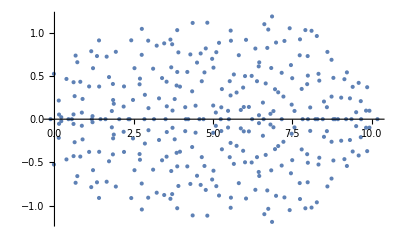

```mathematica
ListPlot[ReIm[Eigenvalues[ A]],PlotRange->All]
```

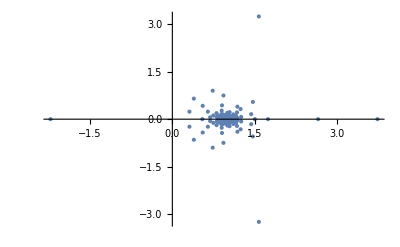

```mathematica
ListPlot[ReIm[Eigenvalues[Inverse[U].Inverse[L]. A]],PlotRange->All]
```

```mathematica
Options[SparseArray`SparseMatrixILU]
```

{SparseArray`FillIn→Automatic,Method→ILUT,SparseArray`PermutationTolerance→Automatic,Tolerance→Automatic}

```mathematica
n=124;
nz=3n;
A=SparseArray[Band[{1,1}]:> RandomReal[{0.1,10}],{n,n}];
Do[ {i,j}=RandomInteger[{1,n},{2}];
A⟦i,j⟧+=RandomReal[{-1,1}],
{nz}]
{LU,p}=SparseArray`SparseMatrixILU[A,SparseArray`FillIn->132];
L=LowerTriangularize[LU,-1]+IdentityMatrix[n];
U=UpperTriangularize[LU];
TabView[Map[MatrixPlot,Normal[{A,L,U}]]]
```

123